Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 5

Metoda kolejnych przybliżeń

## Równanie Fredholma II rodzaju

### Zadanie 1

Wyznaczyć metodą kolejnych przybliżeń rozwiązanie przybliżone y_n równania

y(x)=ⅇ^x-1/4∫_0^1 (x ⅇ^t y(t))ⅆt

Argument:  n

Sprawdzić, czy metodę można zastosować. 
Wyznaczyć rozwiązanie dla kilku wartości n. 
Na tej podstawie odgadnąć rozwiązanie dokładne i sprawdzić jego poprawność.

### Zadanie 2

Wyznaczyć rozwiązania przybliżone y_n dla  n=2,4,6,8, równania:

y(x)=sin x + (x-1)/4+1/4∫_0^(π/2) (t-x)  y(t)ⅆt.

Utworzyć wykresy porównujące rozwiązanie przybliżone z rozwiązaniem dokładnym, którym jest funkcja y(x)=sin x, np.  w postaci:

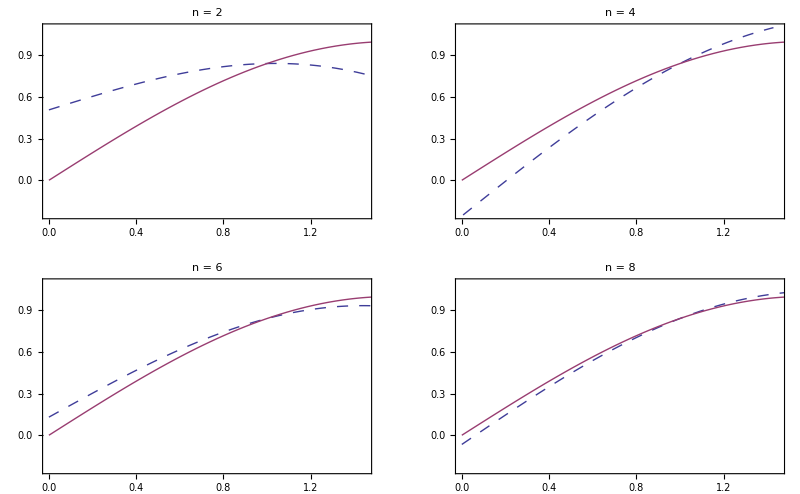

## Rozwiązanie

### Kod procedury

Procedura realizuje Metodę kolejnych przybliżeń dla równań postaci: y(x)==f(x)+λ∫_a^b K(x,t)y(t)dt.
Wejście:
	f - zadana funkcja f(x);
	Ker - jądro równania K(x,t);
	λ - zadana liczba;
	a, b - granice całkowania;
	n - zadana liczba naturalna;
	z - argument zwracanej funkcji.
Wyjście:
	n-ta suma częściowa będąca rozwiązaniem przybliżonym.

```mathematica
Clear[mkp];
mkp[f_,Ker_,λ_,a_,b_,n_Integer?NonNegative,z_Symbol]:=Module[{M,φ,yn,wynik},
(* Sprawdzenie, czy metodę można zastosować *)
M=Maximize[{Ker[x,t],0≤x≤1&&0≤t≤1},{x,t}]⟦1⟧;
If[Abs[λ]>=1/(M (b-a)),Return["Metody nie można zastosować"]];

(* Zależności na funkcje Subscript[φ, m], m liczba naturalna *)
φ[0][x_]:=f[x];
φ[m_][x_]:=∫_a^b Ker[x,t]*(φ[m-1][x]/.{x->t})ⅆt;

(* Suma częściowa jako przybliżone rozwiązanie równania *)
yn[m_][x_]:=Simplify[∑_(i=0)^m λ^i φ[i][x]];
wynik=Table[Simplify[yn[j][z]],{j,0,n}];

Return[yn[n][z]]
]
```

### Zadanie 1.

```mathematica
Clear[f,Ker,λ,a,b,n];
f[x_]:=Exp[x];Ker[x_,t_]:=x ⅇ^t;λ=-1/4;a=0;b=1;n=15;
(* Sprawdzimy postaci kolejnych 15 rozwiązań przybliżonych *)
Do[Print[mkp[f,Ker,λ,a,b,i,z]],{i,n}]
```

ⅇ^z-1/8 (-1+ⅇ^2) z

ⅇ^z-3/32 (-1+ⅇ^2) z

ⅇ^z-13/128 (-1+ⅇ^2) z

ⅇ^z-51/512 (-1+ⅇ^2) z

ⅇ^z-(205 (-1+ⅇ^2) z)/2048

ⅇ^z-(819 (-1+ⅇ^2) z)/8192

ⅇ^z-(3277 (-1+ⅇ^2) z)/32768

ⅇ^z-(13107 (-1+ⅇ^2) z)/131072

ⅇ^z-(52429 (-1+ⅇ^2) z)/524288

ⅇ^z-(209715 (-1+ⅇ^2) z)/2097152

ⅇ^z-(838861 (-1+ⅇ^2) z)/8388608

ⅇ^z-(3355443 (-1+ⅇ^2) z)/33554432

ⅇ^z-(13421773 (-1+ⅇ^2) z)/134217728

ⅇ^z-(53687091 (-1+ⅇ^2) z)/536870912

ⅇ^z-(214748365 (-1+ⅇ^2) z)/2147483648

```mathematica
214748365/2147483648//N
```

0.1

Czyżby rozwiązaniem była funkcja

```mathematica
ⅇ^x-1/10 (ⅇ^2-1) x
```

?

Weryfikujemy:

```mathematica
ⅇ^x-1/10 (ⅇ^2-1) x==f[x]+λ Integrate[Ker[x,t]*(ⅇ^t-1/10 (ⅇ^2-1) t),{t,a,b}]
```

True

### Zadanie 2.

```mathematica
Clear[f,Ker,λ,a,b,przyblizone];
f[x_]:=Sin[x]+(x-1)/4;Ker[x_,t_]:=t-x;λ=1/4;a=0;b=π/2;
przyblizone=Table[mkp[f,Ker,λ,a,b,i,z],{i,2,8,2}]
```

{(π^4-π^4 z+12288 Sin[z])/12288,(π^8 (-1+z))/37748736+Sin[z],-(π^12 (-1+z))/115964116992+Sin[z],(π^16 (-1+z))/356241767399424+Sin[z]}

```mathematica
wykres2=Plot[{Sin[z],przyblizone[[1]]},{z,a,b},PlotLegends->{"sin(x)","y_2"},PlotStyle->{LightRed,Dashed}];
wykres4=Plot[{Sin[z],przyblizone[[2]]},{z,a,b},PlotLegends->{"sin(x)","y_4"},PlotStyle->{LightRed,Dashed}];
wykres6=Plot[{Sin[z],przyblizone[[3]]},{z,a,b},PlotLegends->{"sin(x)","y_6"},PlotStyle->{LightRed,Dashed}];
wykres8=Plot[{Sin[z],przyblizone[[4]]},{z,a,b},PlotLegends->{"sin(x)","y_8"},PlotStyle->{LightRed,Dashed}];
GraphicsGrid[{{wykres2,wykres4},{wykres6,wykres8}}]
```

-Graphics-